```mathematica
(*Příklad č.6*)
Solve[a*x^2+5x+2==0,x]
```

{{x→(-5-√(25-8 a))/(2 a)},{x→(-5+√(25-8 a))/(2 a)}}

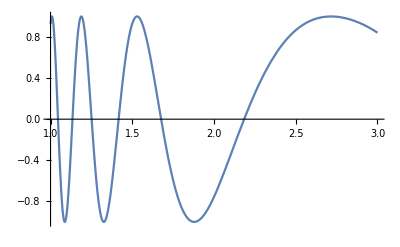

```mathematica
y=Sin[x^2]/.x->(-5-√(25-8 a))/(2 a);
Plot[y,{a,1,3}]
```

```mathematica
(*Příklad č.7*)
Abs[(3+4I)+(4+5I)]
```

√130

```mathematica
(*Příklad č.8*)
(*Částka v Kč, kterou banka připíše za 30 dní*)
urok=0.1;
dni=30;
du[castka_]:=castka*urok/100/365;
duz[castka_]:=Floor[du[castka],0.01];
nextday[castka_]:=Floor[(castka+duz[castka]),0.01];
(*Použití fce Nest na fci nextday*)
Nest[nextday,10000,dni]
```

10000.6

```mathematica
(*Částka v Kč, kterou banka vydělá*)
nextday2[castka_]:=(castka+du[castka]);
Nest[nextday2,10000,dni]-Nest[nextday,10000,dni]
```

0.22195